```mathematica
x = 10^-3*{0,1.0,1.5,2.0,2.5,3.0,3.5,4.0,4.5,5.0,5.5,6.0,6.5,7.0,7.5,8.0,8.5,9.0,9.5,10.0,10.5,11.0,11.5,12.0,12.5,13.0}; (*m*)
P = 10^-3*{1.34,1.34,1.34,1.32,1.29,1.24,1.18,1.12,1.04,0.95,0.85,0.74,0.63,0.52,0.42,0.33,0.26,0.195,0.145,0.11,0.08,0.055,0.038,0.026,0.017,0.011};(*W*)
data={};
For[i=1, i<Length[x]+1, i++, 
AppendTo[data, {x[[i]], P[[i]]}];
]
data
```

{{0,0.00134},{0.001,0.00134},{0.0015,0.00134},{0.002,0.00132},{0.0025,0.00129},{0.003,0.00124},{0.0035,0.00118},{0.004,0.00112},{0.0045,0.00104},{0.005,0.00095},{0.0055,0.00085},{0.006,0.00074},{0.0065,0.00063},{0.007,0.00052},{0.0075,0.00042},{0.008,0.00033},{0.0085,0.00026},{0.009,0.000195},{0.0095,0.000145},{0.01,0.00011},{0.0105,0.00008},{0.011,0.000055},{0.0115,0.000038},{0.012,0.000026},{0.0125,0.000017},{0.013,0.000011}}

{P0→0.00137344,ω→0.00508653,z0→0.00625922}

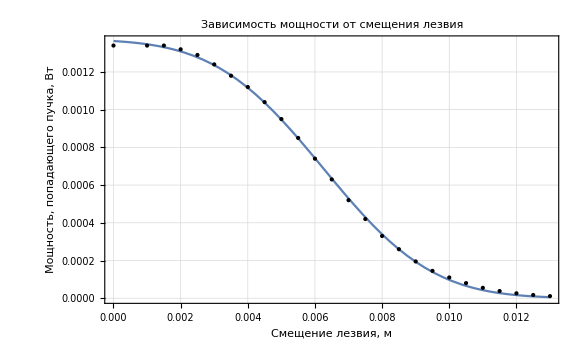

```mathematica
model = P0/2*(1 - Erf[(Sqrt[2]*(z - z0))/ω]);
fit = FindFit[data, model, {P0, ω, z0}, z]
modelf = Function[{z}, Evaluate[model /. fit]];
Plot[modelf[z], {z, 0, 0.013}, Epilog->Map[Point, data], Frame->True, FrameLabel->{"Смещение лезвия, м", "Мощность, попадающего пучка, Вт"}, PlotLabel->"Зависимость мощности от смещения лезвия", GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]]
P01 = 0.0013734; (*W*)
ω1 = 0.00508653; (*m*)
z1 = 0.0062592; (*m*)
```

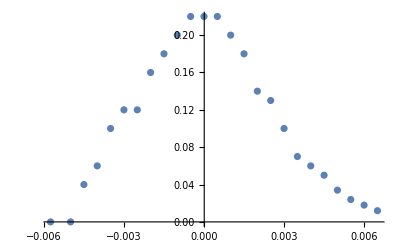

{A→0.21882,ω2→0.00491475}

Function[{ρ},0.21882 ⅇ^(-82799.4 ρ^2)]

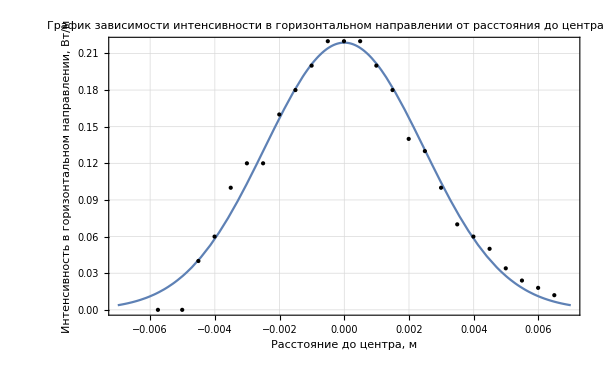

```mathematica
data1 = {};
For[i=1, i<Length[P], i++, 
AppendTo[data1, {(x[[i+1]]+x[[i]])/2 - z1, -(P[[i+1]]-P[[i]])/(x[[i+1]]-x[[i]])}]
]
ListPlot[data1]
modelI = A Exp[(-2 ρ^2)/ω2^2];
fitI = FindFit[data1, modelI, {A, ω2}, ρ]

modelfI = Function[{ρ}, Evaluate[modelI /. fitI]]
Plot[modelfI[ρ], {ρ, -0.007, 0.007}, Epilog->Map[Point, data1], PlotLabel->"График зависимости интенсивности в горизонтальном направлении от расстояния до центра пучка", Frame->True, FrameLabel->{  "Расстояние до центра, м","Интенсивность в горизонтальном направлении, Вт/м"}, GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]]
```

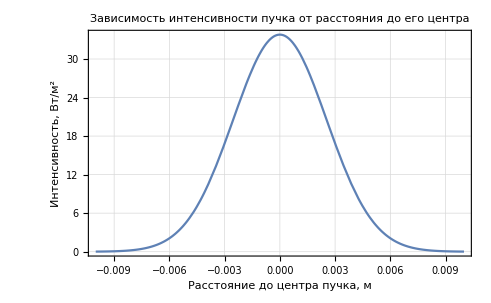

```mathematica
P01 = 0.0013734; (*W*)
ω1 = 0.00508653; (*m*)
z1 = 0.0062592; (*m*)

Intensity = (2P01)/(Pi ω1^2)*Exp[(-2 r^2)/ω1^2];
Plot[Intensity, {r, -0.010, 0.010}, FrameLabel->{"Расстояние до центра пучка, м", "Интенсивность, Вт/(:043c)^2"}, PlotLabel->"Зависимость интенсивности пучка от расстояния до его центра", Frame->True, GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed]]
```